# Simple Acoustic Data Acquisition for Mathematica

## WJ Turkel, June 28, 2011

### How it works

The changing voltage from a sensor or transducer of some sort is fed into a circuit that makes audible chirps or clicks.  The frequency of the clicks depends on the signal voltage.   The audio is recorded and the signal subsequently processed in Mathematica, to extract a record of the changing voltage.  We do this by counting the number of clicks that occur in a given period.

### Voltage-to-frequency circuit

This is basically a metronome or tone generator, depending on the values of the variable resistor and capacitor.  The frequency of chirps is determined by signal voltages ranging between approximately 1.25 and 4.70 volts.  Adjust the variable resistor to tune the frequency range.  Increasing the value of the capacitor decreases frequency and increases the duration of individual events.  Decreasing the capacitor increases frequency and makes each pulse or click shorter.  The circuit can be modified so it is powered by 9 volts.  The piezo element that I used is rated for 3-20 volts, 10 mA.  For the test here, the variable resistor was set to 100K, measured with a DMM.

### A signal

When the piezo element is placed near the microphone of a computer, the signal can be recorded for processing.  If the platform supports it, sounds can be directly recorded using Mathematica's SystemDialogInput["RecordSound"] command.  Macs don't support that, however, so you have to record using a program like Audacity, then Import the audio file if you are on a Mac.

To make the recording below, I hooked up the signal line to a power supply set at 4.7v, decreased it to 1.25v by hand, and then increased it back to 4.7v.  Lower voltages map on to higher frequencies.

The path to audio files.

```mathematica
path="/Users/wjt/Desktop/";
```

We can import the signal in a form where it can be played back as an audio file.

```mathematica
rawSignal=Import[path<>"sample-data.wav"];
```

```mathematica
rawSignal
```

-Graphics-

We can see that our sample rate is 44100 samples per second.  From this we can calculate the duration of each data point, and the number of data points in one millisecond (about 44).

```mathematica
sampleRate=44100
```

44100

```mathematica
pointDuration=N[1/sampleRate]
```

0.0000226757

```mathematica
second=44100;
msec=N[second/1000]
```

44.1

For processing, we want to import the signal as data.

```mathematica
signalData=Flatten@Import[path<>"sample-data.wav","Data"];
```

```mathematica
Length[signalData]
```

846080

We can get some idea of what the signal looks like by plotting every thousandth point.  Note that individual clicks may or may not be sampled, since each is only a few hundred points long.

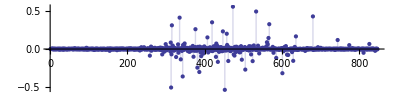

```mathematica
ListLinePlot[signalData⟦1;;Length[signalData];;1000⟧,ImageSize->Full,AspectRatio->0.25,PlotRange->All,Joined->False,Filling->Axis]
```

### Start by exploring a region where clicks are sparse

Near the beginning of the recording, clicks are relatively infrequent.  We want to plot every point in a region where a click has occurred.  If we start at the 3 second mark and look at 50 milliseconds of our data, we can see one click.

```mathematica
sparseRegion=signalData⟦(3*second);;(3*second)+Round[50*msec]⟧;
```

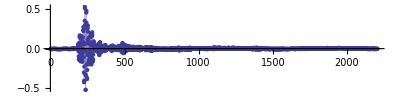

```mathematica
ListLinePlot[sparseRegion,ImageSize->Full,AspectRatio->0.25,PlotRange->All,Joined->False,Filling->Axis]
```

We are interested in finding peaks, so we will take the absolute value of our data.  We can also use the MovingAverage command to smooth the data a bit.  Averaging over ten points seems to give us a sharp peak.

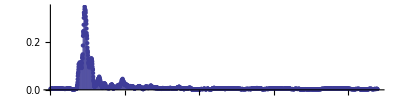

```mathematica
ListLinePlot[MovingAverage[Abs[sparseRegion],10],ImageSize->Full,AspectRatio->0.25,PlotRange->All,Joined->False,Filling->Axis]
```

Since we are only interested in counting clicks, we can make a thresholding function that returns 1 when the signal is above a given level and zero otherwise.

```mathematica
thresholdFunction[value_,threshold_]:=
If[value>threshold,1,0]
```

Now we can plot our thresholded region.  We use the Map command to apply the function to each data point.

```mathematica
threshold = 0.25;
```

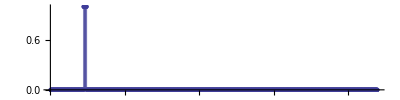

```mathematica
ListLinePlot[Map[thresholdFunction[#,threshold]&,MovingAverage[Abs[sparseRegion],10]],ImageSize->Full,AspectRatio->0.25,PlotRange->All,Joined->False,Filling->Axis]
```

### Now we need to look at a region where clicks are dense

The processing that we've done so far looks like it will pull the click out of a region of the data where they are sparse.  We need to make sure it will also work for regions where the clicks are dense.  We look at a 50 millisecond-long region 10 seconds into the data.

```mathematica
denseRegion=signalData⟦(10*second);;(10*second)+Round[50*msec]⟧;
```

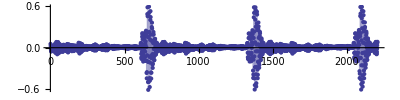

```mathematica
ListLinePlot[denseRegion,ImageSize->Full,AspectRatio->0.25,PlotRange->All,Joined->False,Filling->Axis]
```

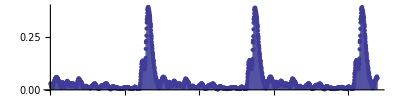

```mathematica
ListLinePlot[MovingAverage[Abs[denseRegion],10],ImageSize->Full,AspectRatio->0.25,PlotRange->All,Joined->False,Filling->Axis]
```

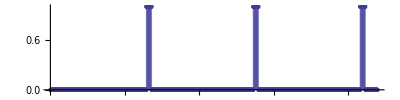

```mathematica
ListLinePlot[Map[thresholdFunction[#,threshold]&,MovingAverage[Abs[denseRegion],10]],ImageSize->Full,AspectRatio->0.25,PlotRange->All,Joined->False,Filling->Axis]
```

### Create thresholded version of whole data set

Since our thresholding looks like it will work nicely for our data, we can apply it to the whole dataset.

```mathematica
signalThresholded=Map[thresholdFunction[#,threshold]&,MovingAverage[Abs[signalData],10]];
```

```mathematica
Length[signalThresholded]
```

846071

Quickly look at sparse and dense regions

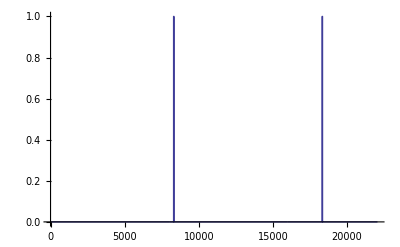

```mathematica
ListLinePlot[signalThresholded⟦second;;second+Round[500*msec]⟧]
```

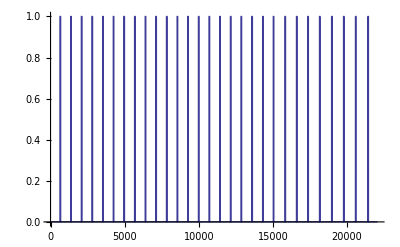

```mathematica
ListLinePlot[signalThresholded⟦(10*second);;(10*second)+Round[500*msec]⟧]
```

### Partition data into short, overlapping windows, and count clicks in each

We use the Partition command to partition our data into short, overlapping windows.

```mathematica
signalThresholdedPartition=Partition[signalThresholded,Round[200*msec],Round[100*msec]];
```

This gives us 190 windows to count clicks in.

```mathematica
Length[signalThresholdedPartition]
```

190

Now we need a function to count the number of clicks in a window.  Each click will be a string of 1s separated on either side by a string of 0s.  We can't count on each click being the same length, however.

We use the Split command to split each window into runs of similar characters, and then Map the Total function over each of the resulting lists

```mathematica
Split[{0,0,0,1,1,1,0,0}]
```

{{0,0,0},{1,1,1},{0,0}}

```mathematica
Map[Total,Split[{0,0,0,1,1,1,0,0}]]
```

{0,3,0}

Now we simply need to say that if the resulting total is more than some small threshold (say 5) we count it as a click.  That way we don't count stray events that aren't part of a click.

```mathematica
countClicks[window_]:=
Total[Map[If[#>5,1,0]&,Map[Total,Split[window]]]]
```

### Reconstructing the input voltage

How well does our click-counting function work?

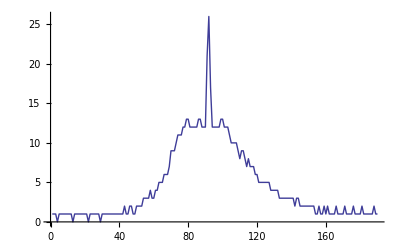

```mathematica
ListLinePlot[Map[countClicks,signalThresholdedPartition]]
```

From this curve we can see that the voltage started out high, dropped, and then increased again.  Note the spike in the middle, which represents a very dense cluster of clicks.  Looking at the raw signal, we see what appears to be a burst of noise in the middle.  If this was actually noise, rather than a low voltage, we could edit the data to remove it.  At this point, we would also want to calibrate the incoming voltages with the recorded frequency.

### References

I used the V-to-F Converter on page 51 of Mims, Science and Communication Circuits and Projects and the Audio Oscillator / Metronome on page 22 of Mims, Timer, Op Amp and Optoelectronic Circuits and Projects as the starting point for this circuit.